# Constructive Tree-Level Diagrams

This notebook generates tree-level constructive Feynman diagrams and their amplitudes from a HEPCAT model.

The previous generate-and-test approach enumerated Prufer trees, then tried every external permutation and every Standard-Model particle on every internal line, and finally removed duplicates with graph isomorphism. That is correct but extremely slow.

This rewrite builds diagrams the way MadGraph does: labeled external currents are recursively fused through model vertices. Internal particles are determined by the Feynman rules, so invalid flavor assignments are never created. Each function is defined once.

Public API:
  CreateDiagrams[p1, p2, ..., model]
  CreateArrowDiagram[diag]  (options: "ShowVertexExpressions", "ShowPropagatorExpressions")
  CreateArrowDiagrams[{diag1, diag2, ...}]
  diagramAmplitude[diag]
  diagramAmplitudes[{diag1, diag2, ...}]

## Setup

Load HEPCAT and a model.  Model 1 is the SM; model 2 is QED.

```mathematica
HEPCATBasePath = "~/code/hepcat";
```

```mathematica
$HEPCATpath = HEPCATBasePath <> "/source/";
Get[$HEPCATpath <> "HEPCAT.wl"]
```

```mathematica
sm = ReadModel[HEPCATBasePath <> "/models", 1];
```

## Implementation

Algorithm. Start with one current per external particle. At every step, either
  (1) connect every remaining current with a single model vertex (a complete diagram), or
  (2) fuse a subset that includes the lowest-index current, producing a new off-shell current, and recurse.
Feynman rules, propagators, and spin indices are attached afterwards. Tree uniqueness is decided by the bipartition of external legs on each internal line, so graph isomorphism is not needed.

```mathematica
(*
  Constructive tree-level diagram generator.

  Tree diagrams are built by recursively combining currents through
  model vertices, the same strategy MadGraph uses.  External legs are
  labeled from the start, so there is no n! leaf permutation, no
  enumeration of unlabeled Prufer trees, and no scan over the full
  SM particle list for every internal line.
*)

(* Model lookup tables.  Built locally from the model argument of
   each CreateDiagrams call, so multiple models (e.g. sm and qed) can
   be used in the same notebook without shared state. *)

buildModelData[model_] := Module[
  {names, nameQ, anti, mass, rank, vertices, bySorted, combineLookup},
  names = DeleteDuplicates @ Flatten[model[[1, All, {2, 3}]]];
  nameQ = AssociationThread[names, True];
  anti = Association @ Flatten[
    {#[[2]] -> #[[3]], #[[3]] -> #[[2]]} & /@ model[[1]],
    1
  ];
  mass = Association @ Flatten[
    {#[[2]] -> #[[6]], #[[3]] -> #[[6]]} & /@ model[[1]],
    1
  ];
  rank = AssociationThread[names, Range @ Length[names]];
  vertices = DeleteCases[
    Map[
      Function[vrow,
        Module[{ps},
          ps = TakeWhile[vrow, KeyExistsQ[nameQ, #] &];
          If[Length[ps] < 3,
            Nothing,
            <|
              "Particles" -> ps,
              "Sorted" -> Sort[ps],
              "Valence" -> Length[ps],
              "Row" -> vrow,
              "Expression" -> I*vrow[[-2]]*vrow[[-1]]
            |>
          ]
        ]
      ],
      model[[2]]
    ],
    Nothing
  ];
  bySorted = GroupBy[vertices, #["Sorted"] &];
  combineLookup = Merge[
    Flatten[
      Table[
        Module[{ps = vertices[[j, "Particles"]], nv},
          nv = Length[ps];
          Table[
            {nv - 1, Sort[Delete[ps, i]]} -> {ps[[i]]},
            {i, nv}
          ]
        ],
        {j, Length[vertices]}
      ],
      1
    ],
    DeleteDuplicates @ Flatten[#] &
  ];
  <|
    "Names" -> names,
    "Anti" -> anti,
    "Mass" -> mass,
    "Rank" -> rank,
    "Vertices" -> vertices,
    "BySorted" -> bySorted,
    "CombineLookup" -> combineLookup,
    "Valences" -> Sort @ DeleteDuplicates[vertices[[All, "Valence"]]]
  |>
];

CreateDiagrams::usage = "CreateDiagrams[p1, p2, ..., model] generates tree-level constructive Feynman diagrams for the process with external particles p1, p2, ... in a HEPCAT model.";
CreateArrowDiagram::usage = "CreateArrowDiagram[diag] draws a labeled tree diagram. Options: \"ShowVertexExpressions\", \"ShowPropagatorExpressions\".";
CreateArrowDiagrams::usage = "CreateArrowDiagrams[{diag1, diag2, ...}] draws a list of diagrams.";
diagramAmplitude::usage = "diagramAmplitude[diag] returns the constructive amplitude of a single diagram, including propagator and spin-index structure.";
diagramAmplitudes::usage = "diagramAmplitudes[{diag1, diag2, ...}] maps diagramAmplitude over a list of diagrams.";

tagParticles[particles_List] := Module[{seen = <||>},
  MapIndexed[
    Function[{p, i},
      seen[p] = Lookup[seen, p, 0] + 1;
      <|"Particle" -> p, "ID" -> seen[p], "InputIndex" -> First[i]|>
    ],
    particles
  ]
];

multiparticleOf[inds_List] := Multiparticle @@ Sort[inds];

(*Current algebra*)

emptyCurrent[particle_, index_] := <|
  "Particle" -> particle,
  "Externals" -> {index},
  "Root" -> index,
  "InternalVertices" -> {},
  "Edges" -> {},
  "InternalEdges" -> {},
  "EdgeLabels" -> <||>,
  "EdgeOrientation" -> <||>,
  "EdgeIndices" -> <||>
|>;

orientationOf[edge_, labels_, md_] := Module[
  {ends, p1, p2, r1, r2, canon, antiCanon, vCanon, vAnti},
  ends = List @@ edge;
  p1 = labels[ends[[1]]];
  p2 = labels[ends[[2]]];
  r1 = Lookup[md["Rank"], p1, Infinity];
  r2 = Lookup[md["Rank"], p2, Infinity];
  If[r1 <= r2,
    canon = p1; antiCanon = p2; vCanon = ends[[1]]; vAnti = ends[[2]],
    canon = p2; antiCanon = p1; vCanon = ends[[2]]; vAnti = ends[[1]]
  ];
  <|
    "Particle" -> canon,
    "Antiparticle" -> antiCanon,
    "ParticleVertex" -> vCanon,
    "AntiparticleVertex" -> vAnti
  |>
];

(* Glue currents onto a new vertex. leftoverP is the particle this vertex
   consumes on the outgoing line, or None if this vertex completes the diagram. *)
glueCurrents[currents_List, leftoverP_, nextId_, fullExternals_List, md_] := Module[
  {newV, anti = md["Anti"], newEdges, newInternal, newLabels, newOrients, newIndices,
   mergedVerts, mergedEdges, mergedInternal, mergedLabels, mergedOrients, mergedIndices,
   allExt, pAtNew, pAtOld, edge, labels, c},
  newV = nextId;
  allExt = Sort[fullExternals];
  newEdges = {};
  newInternal = {};
  newLabels = <||>;
  newOrients = <||>;
  newIndices = <||>;
  Do[
    c = currents[[i]];
    edge = UndirectedEdge @@ Sort[{c["Root"], newV}];
    AppendTo[newEdges, edge];
    If[c["InternalVertices"] =!= {},
      pAtNew = c["Particle"];
      pAtOld = Lookup[anti, pAtNew, pAtNew];
      labels = <|newV -> pAtNew, c["Root"] -> pAtOld|>;
      AppendTo[newInternal, edge];
      newLabels[edge] = labels;
      newOrients[edge] = orientationOf[edge, labels, md];
      newIndices[edge] = <|
        newV -> multiparticleOf[c["Externals"]],
        c["Root"] -> multiparticleOf[Complement[allExt, c["Externals"]]]
      |>
    ];
    ,
    {i, Length[currents]}
  ];
  mergedVerts = Join[Flatten[currents[[All, "InternalVertices"]]], {newV}];
  mergedEdges = Join[Flatten[currents[[All, "Edges"]]], newEdges];
  mergedInternal = Join[Flatten[currents[[All, "InternalEdges"]]], newInternal];
  mergedLabels = Join @@ Append[currents[[All, "EdgeLabels"]], newLabels];
  mergedOrients = Join @@ Append[currents[[All, "EdgeOrientation"]], newOrients];
  mergedIndices = Join @@ Append[currents[[All, "EdgeIndices"]], newIndices];
  <|
    "Particle" -> If[leftoverP === None, None, Lookup[anti, leftoverP, leftoverP]],
    "Externals" -> Sort[Join @@ currents[[All, "Externals"]]],
    "Root" -> newV,
    "InternalVertices" -> mergedVerts,
    "Edges" -> mergedEdges,
    "InternalEdges" -> mergedInternal,
    "EdgeLabels" -> mergedLabels,
    "EdgeOrientation" -> mergedOrients,
    "EdgeIndices" -> mergedIndices
  |>
];

diagramKey[curr_] := Sort @ KeyValueMap[
  Function[{edge, labels},
    {
      Sort[List @@ curr["EdgeIndices"][edge]],
      KeySort @ Association @ KeyValueMap[
        Function[{v, p}, curr["EdgeIndices"][edge][v] -> p],
        labels
      ]
    }
  ],
  curr["EdgeLabels"]
];

(*Recursive generation*)

generateRawDiagrams[ext_List, md_] := Module[
  {n, fullExternals, startCurrents, combineLookup, fuse, collected},
  n = Length[ext];
  If[n < 3, Return[{}]];
  fullExternals = Range[n];
  startCurrents = MapThread[emptyCurrent[#1, #2] &, {ext, fullExternals}];
  combineLookup = md["CombineLookup"];
  collected = First[
    Reap[
      fuse[currents_, nextId_] := Module[
        {nc, parts, distPos, distinguished, others, subsets, chosen, remaining, lefts},
        nc = Length[currents];
        parts = currents[[All, "Particle"]];
        If[Lookup[md["BySorted"], Key[Sort[parts]], {}] =!= {},
          Sow[glueCurrents[currents, None, nextId, fullExternals, md], "diag"]
        ];
        If[nc <= 3, Return[]];
        distPos = First @ Ordering[Min /@ currents[[All, "Externals"]]];
        distinguished = currents[[distPos]];
        others = Delete[currents, distPos];
        Do[
          subsets = Subsets[Range @ Length[others], {k}];
          Do[
            chosen = Prepend[others[[subsets[[si]]]], distinguished];
            remaining = others[[Complement[Range @ Length[others], subsets[[si]]]]];
            lefts = Lookup[
              combineLookup,
              Key[{Length[chosen], Sort[chosen[[All, "Particle"]]]}],
              {}
            ];
            Do[
              fuse[
                Prepend[remaining, glueCurrents[chosen, lefts[[li]], nextId, fullExternals, md]],
                nextId + 1
              ],
              {li, Length[lefts]}
            ],
            {si, Length[subsets]}
          ],
          {k, 1, nc - 3}
        ]
      ];
      fuse[startCurrents, n + 1];,
      "diag"
    ][[2]],
    {}
  ];
  DeleteDuplicatesBy[collected, diagramKey]
];

(*Feynman rules*)

replaceVertexIndices[expr_, slotRules_Association] := expr /. {
  Spinor[a___, i_Integer] /; KeyExistsQ[slotRules, i] :> Spinor[a, slotRules[i]],
  xFactor[i_Integer, j_Integer] /; KeyExistsQ[slotRules, i] && KeyExistsQ[slotRules, j] :>
    xFactor[slotRules[i], slotRules[j]],
  xTildeFactor[i_Integer, j_Integer] /; KeyExistsQ[slotRules, i] && KeyExistsQ[slotRules, j] :>
    xTildeFactor[slotRules[i], slotRules[j]]
};

legParticles[legs_List] := Map[#["Particle"] &, legs];

vertexRowMatches[incidentLegs_List, rowParticles_List] :=
  Select[Permutations[incidentLegs], legParticles[#] === rowParticles &];

vertexIncidentLegData[vertex_, neighbors_List, extMap_, edgeLabels_, edgeIndices_, leafSet_] :=
  Map[
    Function[neighbor,
      If[KeyExistsQ[extMap, neighbor],
        <|
          "Particle" -> extMap[neighbor, "Particle"],
          "Index" -> extMap[neighbor, "InputIndex"],
          "Kind" -> "External",
          "Source" -> neighbor
        |>,
        Module[{edge = UndirectedEdge @@ Sort[{vertex, neighbor}]},
          <|
            "Particle" -> edgeLabels[edge][vertex],
            "Index" -> edgeIndices[edge][vertex],
            "Kind" -> "Internal",
            "Source" -> edge
          |>
        ]
      ]
    ],
    neighbors
  ];

vertexStructureInstances[vertex_, incidentLegs_, md_] := Module[
  {sorted, rows},
  sorted = Sort[legParticles[incidentLegs]];
  rows = Lookup[md["BySorted"], Key[sorted], {}];
  Flatten[
    Map[
      Function[row,
        Map[
          Function[ordered,
            <|
              "Vertex" -> vertex,
              "IncidentLegs" -> ordered,
              "ModelRow" -> row["Row"],
              "SlotRules" -> AssociationThread[Range @ Length[ordered], Map[#["Index"] &, ordered]],
              "Expression" -> replaceVertexIndices[row["Expression"],
                AssociationThread[Range @ Length[ordered], Map[#["Index"] &, ordered]]]
            |>
          ],
          vertexRowMatches[incidentLegs, row["Particles"]]
        ]
      ],
      rows
    ],
    1
  ]
];

internalPropagatorData[edgeLabels_, edgeIndices_, edgeOrientation_, md_] :=
  Association @ KeyValueMap[
    Function[{edge, labels},
      Module[{orient, particle, index, mass},
        orient = edgeOrientation[edge];
        particle = orient["Particle"];
        index = First[Values[edgeIndices[edge]]];
        mass = Lookup[md["Mass"], particle, Missing["MassNotFound"]];
        edge -> <|
          "Particle" -> particle,
          "Antiparticle" -> orient["Antiparticle"],
          "ParticleVertex" -> orient["ParticleVertex"],
          "AntiparticleVertex" -> orient["AntiparticleVertex"],
          "Index" -> index,
          "Mass" -> mass,
          "Factor" -> If[MissingQ[mass],
            Missing["MassNotFound", particle],
            I/PropDen[Mom[index], mass]
          ]
        |>
      ]
    ],
    edgeLabels
  ];

attachFeynmanRules[raw_, ext_List, md_] := Module[
  {n, tags, extMap, leafVerts, graph, adj, incident, structures, props, v, nbrs},
  n = Length[ext];
  tags = tagParticles[ext];
  extMap = AssociationThread[Range[n], tags];
  leafVerts = Range[n];
  graph = Graph[
    Join[leafVerts, raw["InternalVertices"]],
    raw["Edges"],
    VertexLabels -> None
  ];
  adj = AssociationMap[AdjacencyList[graph, #] &, raw["InternalVertices"]];
  incident = AssociationMap[
    Function[v,
      vertexIncidentLegData[
        v, adj[v], extMap, raw["EdgeLabels"], raw["EdgeIndices"], leafVerts
      ]
    ],
    raw["InternalVertices"]
  ];
  structures = AssociationMap[
    vertexStructureInstances[#, incident[#], md] &,
    raw["InternalVertices"]
  ];
  If[!AllTrue[Values[structures], Length[#] > 0 &], Return[Nothing]];
  props = internalPropagatorData[raw["EdgeLabels"], raw["EdgeIndices"], raw["EdgeOrientation"], md];
  <|
    "Graph" -> graph,
    "ExternalAssignment" -> extMap,
    "InternalEdgeData" -> Association @ KeyValueMap[
      Function[{edge, labels},
        edge -> Join[
          raw["EdgeOrientation"][edge],
          <|"EndpointLabels" -> labels|>
        ]
      ],
      raw["EdgeLabels"]
    ],
    "InternalEdgeLabels" -> raw["EdgeLabels"],
    "InternalEdgeOrientation" -> raw["EdgeOrientation"],
    "InternalVertices" -> raw["InternalVertices"],
    "LeafVertices" -> leafVerts,
    "InternalEdgeIndices" -> raw["EdgeIndices"],
    "IncidentLegData" -> incident,
    "VertexStructures" -> structures,
    "Propagators" -> props
  |>
];

CreateDiagrams[externalParticles___String, model_] := Module[
  {ext = {externalParticles}, md, raw},
  If[Length[ext] < 3, Return[{}]];
  md = buildModelData[model];
  raw = generateRawDiagrams[ext, md];
  DeleteCases[attachFeynmanRules[#, ext, md] & /@ raw, Nothing]
];

CreateDiagrams[ext_List, model_] := CreateDiagrams[Sequence @@ ext, model];

(*Spin indices and amplitudes*)

spinorVarianceAtEndpoint[diag_, edge_, vertex_] := Which[
  vertex === diag["InternalEdgeOrientation"][edge, "ParticleVertex"], "Upper",
  vertex === diag["InternalEdgeOrientation"][edge, "AntiparticleVertex"], "Lower",
  True, Missing["InvalidVertex", {edge, vertex}]
];

symmetrizeIndices[expr_, inds_List] := Module[{perms = Permutations[inds]},
  If[Length[inds] <= 1, expr,
    Total[(expr /. Thread[inds -> #]) & /@ perms]/Length[perms]
  ]
];

edgeSpinMultiplicity[diag_, edge_] := Module[{vertices},
  vertices = Keys[diag["InternalEdgeIndices"][edge]];
  Max[
    1,
    Sequence @@ Table[
      Length @ Cases[
        Lookup[Last @ Lookup[diag["VertexStructures"], vertex, {<||>}], "Expression", 1],
        Spinor["Spin", _, diag["InternalEdgeIndices"][edge][vertex]],
        Infinity
      ],
      {vertex, vertices}
    ]
  ]
];

edgeSpinIndexData[diag_] := Module[{edges, multiplicities, starts},
  edges = Keys[diag["InternalEdgeLabels"]];
  If[edges === {}, Return[<||>]];
  multiplicities = edgeSpinMultiplicity[diag, #] & /@ edges;
  starts = Most @ FoldList[Plus, 1, multiplicities];
  AssociationThread[
    edges,
    MapThread[Array[Symbol["i" <> ToString[#]] &, #1, #2] &, {multiplicities, starts}]
  ]
];

makeVertexSpinIndicesExplicit[vertexStructure_Association, vertex_, diag_, edgeIndexData_] := Module[
  {expr, incidentLegs, spinorData, grouped, replacementRules, newExpr},
  expr = vertexStructure["Expression"];
  incidentLegs = diag["IncidentLegData"][vertex];
  spinorData = Cases[
    expr,
    s : Spinor["Spin", sa_, mp_Multiparticle] :> Module[{leg},
      leg = SelectFirst[incidentLegs, #["Kind"] === "Internal" && #["Index"] === mp &];
      If[MissingQ[leg],
        Nothing,
        <|"Spinor" -> s, "SpinType" -> sa, "Multiparticle" -> mp, "Edge" -> leg["Source"]|>
      ]
    ],
    Infinity
  ];
  If[spinorData === {}, Return[vertexStructure]];
  grouped = GroupBy[spinorData, #Edge &];
  replacementRules = Flatten @ KeyValueMap[
    Function[{edge, items},
      Module[{inds, variance},
        inds = Take[edgeIndexData[edge], Length[items]];
        variance = spinorVarianceAtEndpoint[diag, edge, vertex];
        MapThread[
          #1["Spinor"] :> Spinor["Spin", variance, #1["SpinType"], #1["Multiparticle"], #2] &,
          {items, inds}
        ]
      ]
    ],
    grouped
  ];
  newExpr = expr /. replacementRules;
  newExpr = Fold[
    Function[{currentExpr, edge},
      If[Length[grouped[edge]] > 1,
        symmetrizeIndices[currentExpr, Take[edgeIndexData[edge], Length[grouped[edge]]]],
        currentExpr
      ]
    ],
    newExpr,
    Keys[grouped]
  ];
  Join[vertexStructure, <|"Expression" -> newExpr|>]
];

makeDiagramSpinIndicesExplicit[diag_] := Module[{edgeIndexData, newVertexStructures},
  edgeIndexData = edgeSpinIndexData[diag];
  newVertexStructures = Association @ KeyValueMap[
    Function[{vertex, structures},
      vertex -> Replace[
        structures,
        {
          {} :> {},
          list_List :> ReplacePart[
            list,
            -1 -> makeVertexSpinIndicesExplicit[Last[list], vertex, diag, edgeIndexData]
          ]
        }
      ]
    ],
    diag["VertexStructures"]
  ];
  Join[diag, <|"VertexStructures" -> newVertexStructures, "SpinIndices" -> edgeIndexData|>]
];

diagramAmplitude[diag_] := Module[{processed, vertexFactors, propagatorFactors},
  processed = makeDiagramSpinIndicesExplicit[diag];
  vertexFactors = Replace[
    Values[processed["VertexStructures"]],
    {{} :> 1, list_List :> Lookup[Last[list], "Expression", 1]},
    1
  ];
  propagatorFactors = Lookup[Values[processed["Propagators"]], "Factor", 1];
  Times @@ Join[vertexFactors, propagatorFactors]/I
];

diagramAmplitudes[diags_List] := diagramAmplitude /@ diags;

(*Drawing*)

displayParticleName[edge_, internalEdgeLabels_Association] := Module[
  {lab, vals},
  lab = Lookup[internalEdgeLabels, edge, Missing["NotFound"]];
  If[MissingQ[lab],
    "",
    vals = DeleteDuplicates[Values[lab]];
    If[Length[vals] == 1, First[vals], Lookup[lab, First[List @@ edge]]]
  ]
];

arrowDirectionData[edge_, internalEdgeLabels_Association, particleToPrint_: Automatic] := Module[
  {lab, ends, printedParticle, targetVertex, sourceVertex},
  lab = Lookup[internalEdgeLabels, edge, Missing["NotFound"]];
  If[MissingQ[lab] || !AssociationQ[lab], Return[Missing["NotAvailable"]]];
  ends = List @@ edge;
  printedParticle = Replace[particleToPrint, Automatic :> First[DeleteDuplicates[Values[lab]]]];
  targetVertex = SelectFirst[ends, Lookup[lab, #, None] === printedParticle &, Missing["NotFound"]];
  If[MissingQ[targetVertex], Return[Missing["NotAvailable"]]];
  sourceVertex = SelectFirst[ends, # =!= targetVertex &, Missing["NotFound"]];
  If[MissingQ[sourceVertex], Return[Missing["NotAvailable"]]];
  {targetVertex, sourceVertex}
];

midArrowPoints[start_, end_, frac_: 0.22] := Module[{mid = (start + end)/2, vec = end - start},
  {mid - frac vec/2, mid + frac vec/2}
];

Options[CreateArrowDiagram] = {
  "ShowVertexExpressions" -> False,
  "ShowPropagatorExpressions" -> False
};

CreateArrowDiagram[diag_, OptionsPattern[]] := Module[
  {
    graph, extMap, intLabels, propagators, leafVerts, internalVerts, vertexStructures,
    showVertexExpressions, showPropagatorExpressions,
    embeddingGraph, coords, coordOf, edges,
    edgePrimitives, vertexPrimitives, externalLabelPrimitives,
    edgeLabelPrimitives, vertexExpressionPrimitives,
    midpoint, normalOffset, leafSet
  },
  showVertexExpressions = OptionValue["ShowVertexExpressions"];
  showPropagatorExpressions = OptionValue["ShowPropagatorExpressions"];
  graph = diag["Graph"];
  extMap = diag["ExternalAssignment"];
  intLabels = diag["InternalEdgeLabels"];
  propagators = Lookup[diag, "Propagators", <||>];
  vertexStructures = Lookup[diag, "VertexStructures", <||>];
  leafVerts = Lookup[diag, "LeafVertices", Select[VertexList[graph], VertexDegree[graph, #] == 1 &]];
  internalVerts = Lookup[diag, "InternalVertices", Complement[VertexList[graph], leafVerts]];
  leafSet = AssociationThread[leafVerts, True];
  embeddingGraph = Graph[VertexList[graph], EdgeList[graph], GraphLayout -> "SpringElectricalEmbedding"];
  coords = GraphEmbedding[embeddingGraph];
  coordOf = AssociationThread[VertexList[embeddingGraph], coords];
  edges = EdgeList[graph];
  midpoint[p1_, p2_] := (p1 + p2)/2;
  normalOffset[p1_, p2_] := Module[{n = {-(p2 - p1)[[2]], (p2 - p1)[[1]]}},
    0.12 Normalize[If[Norm[n] == 0, {1., 0.}, n]]
  ];
  edgePrimitives = Map[
    Function[edge,
      Module[{u, v, p1, p2, dirData, arrowPts, leaf, inner, pLeaf, pInner, startVertex, endVertex, pStart, pEnd},
        {u, v} = List @@ edge;
        {p1, p2} = coordOf /@ {u, v};
        If[KeyExistsQ[leafSet, u] || KeyExistsQ[leafSet, v],
          leaf = If[KeyExistsQ[leafSet, u], u, v];
          inner = If[leaf === u, v, u];
          pLeaf = coordOf[leaf];
          pInner = coordOf[inner];
          arrowPts = midArrowPoints[pLeaf, pInner];
          {Black, Thick, Line[{pLeaf, pInner}], Arrow[arrowPts]},
          dirData = arrowDirectionData[edge, intLabels];
          If[MissingQ[dirData],
            {Black, Thick, Line[{p1, p2}]},
            {startVertex, endVertex} = dirData;
            pStart = coordOf[startVertex];
            pEnd = coordOf[endVertex];
            arrowPts = midArrowPoints[pStart, pEnd];
            {Black, Thick, Line[{p1, p2}], Arrow[arrowPts]}
          ]
        ]
      ]
    ],
    edges
  ];
  edgeLabelPrimitives = Map[
    Function[edge,
      If[KeyExistsQ[intLabels, edge],
        Module[{p1, p2, pos, particleLabel, propData, propFactor},
          {p1, p2} = coordOf /@ (List @@ edge);
          pos = midpoint[p1, p2] + normalOffset[p1, p2];
          particleLabel = displayParticleName[edge, intLabels];
          propData = Lookup[propagators, edge, Missing["NotFound"]];
          propFactor = If[AssociationQ[propData], Lookup[propData, "Factor", Missing["NotFound"]], Missing["NotFound"]];
          {
            Blue, Text[Style[particleLabel, 14], pos],
            If[showPropagatorExpressions && !MissingQ[propFactor],
              Text[Style[TraditionalForm[propFactor], 11, Darker[Green]], pos + {0, -0.08}],
              Nothing
            ]
          }
        ],
        Nothing
      ]
    ],
    edges
  ];
  vertexPrimitives = {Black, Disk[coordOf /@ internalVerts, 0.03]};
  externalLabelPrimitives = Map[
    Function[v,
      Module[{p, nbr, dir, pos, data, label},
        p = coordOf[v];
        nbr = First[AdjacencyList[graph, v]];
        dir = Normalize[p - coordOf[nbr] /. {0, 0} | {0., 0.} -> {1., 0.}];
        pos = p + 0.12 dir;
        data = Lookup[extMap, v, Missing["NotFound"]];
        label = If[AssociationQ[data], Subscript[data["Particle"], data["InputIndex"]], data];
        Text[Style[label, 14, Black], pos]
      ]
    ],
    leafVerts
  ];
  vertexExpressionPrimitives = If[showVertexExpressions,
    Map[
      Function[v,
        Module[{pos, exprList, shownExpr},
          pos = coordOf[v] + {0, 0.14};
          exprList = Lookup[vertexStructures, v, {}];
          shownExpr = Which[
            exprList === {}, Missing["NotAvailable"],
            KeyExistsQ[First[exprList], "Factor"], First[exprList]["Factor"],
            KeyExistsQ[First[exprList], "Expression"], First[exprList]["Expression"],
            True, Missing["NotAvailable"]
          ];
          If[MissingQ[shownExpr],
            Nothing,
            Text[Style[TraditionalForm[shownExpr], 10, Darker[Red]], pos]
          ]
        ]
      ],
      internalVerts
    ],
    {}
  ];
  Graphics[
    {edgePrimitives, edgeLabelPrimitives, vertexPrimitives, externalLabelPrimitives, vertexExpressionPrimitives},
    PlotRange -> All,
    ImagePadding -> 50,
    ImageSize -> 500
  ]
];

Options[CreateArrowDiagrams] = Options[CreateArrowDiagram];
CreateArrowDiagrams[diags_List, opts : OptionsPattern[CreateArrowDiagram]] :=
  CreateArrowDiagram[#, opts] & /@ diags;
```

## Examples

### Four-point: e E → A A

Two diagrams (t- and u-channel electron exchange).  Same-helicity photons have no s-channel because there is no three-photon vertex.

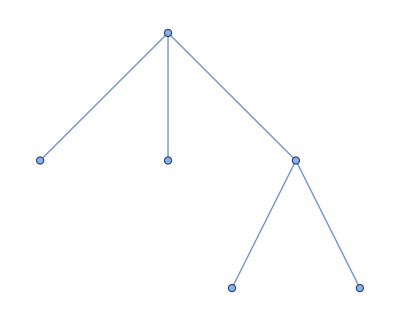
{0.005548,{<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>|>,InternalEdgeData→<|5<->6→<|Particle→e,Antiparticle→E,ParticleVertex→6,AntiparticleVertex→5,EndpointLabels→<|6→e,5→E|>|>|>,InternalEdgeLabels→<|5<->6→<|6→e,5→E|>|>,InternalEdgeOrientation→<|5<->6→<|Particle→e,Antiparticle→E,ParticleVertex→6,AntiparticleVertex→5|>|>,InternalVertices→{5,6},LeafVertices→{1,2,3,4},InternalEdgeIndices→<|5<->6→<|6→Multiparticle[1,3],5→Multiparticle[2,4]|>|>,IncidentLegData→<|5→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→E,Index→Multiparticle[2,4],Kind→Internal,Source→5<->6|>},6→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→e,Index→Multiparticle[1,3],Kind→Internal,Source→5<->6|>}|>,VertexStructures→<|5→{<|Vertex→5,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,4],Kind→Internal,Source→5<->6|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,4],3→3|>,Expression→-ⅈ √2 EE ⟨1P_(2,4)⟩ x_(1,24)|>},6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3],Kind→Internal,Source→5<->6|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3],2→2,3→4|>,Expression→-ⅈ √2 EE ⟨P_(1,3)2⟩ x_(13,2)|>}|>,Propagators→<|5<->6→<|Particle→e,Antiparticle→E,ParticleVertex→6,AntiparticleVertex→5,Index→Multiparticle[1,3],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3)^2)|>|>|>,<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>|>,InternalEdgeData→<|5<->6→<|Particle→e,Antiparticle→E,ParticleVertex→6,AntiparticleVertex→5,EndpointLabels→<|6→e,5→E|>|>|>,InternalEdgeLabels→<|5<->6→<|6→e,5→E|>|>,InternalEdgeOrientation→<|5<->6→<|Particle→e,Antiparticle→E,ParticleVertex→6,AntiparticleVertex→5|>|>,InternalVertices→{5,6},LeafVertices→{1,2,3,4},InternalEdgeIndices→<|5<->6→<|6→Multiparticle[1,4],5→Multiparticle[2,3]|>|>,IncidentLegData→<|5→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→E,Index→Multiparticle[2,3],Kind→Internal,Source→5<->6|>},6→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→e,Index→Multiparticle[1,4],Kind→Internal,Source→5<->6|>}|>,VertexStructures→<|5→{<|Vertex→5,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,3],Kind→Internal,Source→5<->6|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,3],3→4|>,Expression→-ⅈ √2 EE ⟨1P_(2,3)⟩ x_(1,23)|>},6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,4],Kind→Internal,Source→5<->6|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,4],2→2,3→3|>,Expression→-ⅈ √2 EE ⟨P_(1,4)2⟩ x_(14,2)|>}|>,Propagators→<|5<->6→<|Particle→e,Antiparticle→E,ParticleVertex→6,AntiparticleVertex→5,Index→Multiparticle[1,4],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,4)^2)|>|>|>}}

```mathematica
Timing[diags = CreateDiagrams["e", "E", "A.+", "A.+", sm]]
```

```mathematica
Length[diags]
```

```mathematica
CreateArrowDiagrams[diags]
```

{-Graphics-,-Graphics-}

```mathematica
diagramAmplitude[diags[[1]]]
```

-(2 EE^2 ⟨1(P_(2,4))_i1⟩ ⟨(P_(1,3))^i12⟩ x_(1,24) x_(13,2))/(-Me^2+p_(1,3)^2)

### With vertex and propagator expressions

```mathematica
CreateArrowDiagram[diags[[1]], "ShowVertexExpressions" -> True, "ShowPropagatorExpressions" -> True]
```

-Graphics-

### Five-point: e E → A A A

Six diagrams: the three photons can be attached along the fermion line in 3! orders.

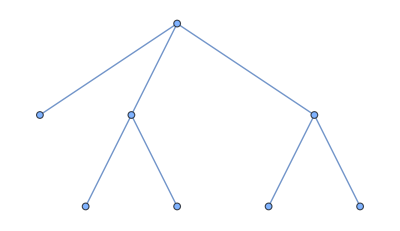
{0.006469,{<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>,5→<|Particle→A.+,ID→3,InputIndex→5|>|>,InternalEdgeData→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,EndpointLabels→<|7→e,6→E|>|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,EndpointLabels→<|8→e,7→E|>|>|>,InternalEdgeLabels→<|6<->7→<|7→e,6→E|>,7<->8→<|8→e,7→E|>|>,InternalEdgeOrientation→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7|>|>,InternalVertices→{6,7,8},LeafVertices→{1,2,3,4,5},InternalEdgeIndices→<|6<->7→<|7→Multiparticle[1,3],6→Multiparticle[2,4,5]|>,7<->8→<|8→Multiparticle[1,3,4],7→Multiparticle[2,5]|>|>,IncidentLegData→<|6→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→E,Index→Multiparticle[2,4,5],Kind→Internal,Source→6<->7|>},7→{<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→e,Index→Multiparticle[1,3],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,5],Kind→Internal,Source→7<->8|>},8→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>,<|Particle→e,Index→Multiparticle[1,3,4],Kind→Internal,Source→7<->8|>}|>,VertexStructures→<|6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,4,5],Kind→Internal,Source→6<->7|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,4,5],3→3|>,Expression→-ⅈ √2 EE ⟨1P_(2,4,5)⟩ x_(1,245)|>},7→{<|Vertex→7,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,5],Kind→Internal,Source→7<->8|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3],2→Multiparticle[2,5],3→4|>,Expression→-ⅈ √2 EE ⟨P_(1,3)P_(2,5)⟩ x_(13,25)|>},8→{<|Vertex→8,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3,4],Kind→Internal,Source→7<->8|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3,4],2→2,3→5|>,Expression→-ⅈ √2 EE ⟨P_(1,3,4)2⟩ x_(134,2)|>}|>,Propagators→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,Index→Multiparticle[1,3],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3)^2)|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,Index→Multiparticle[1,3,4],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3,4)^2)|>|>|>,<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>,5→<|Particle→A.+,ID→3,InputIndex→5|>|>,InternalEdgeData→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,EndpointLabels→<|7→e,6→E|>|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,EndpointLabels→<|8→e,7→E|>|>|>,InternalEdgeLabels→<|6<->7→<|7→e,6→E|>,7<->8→<|8→e,7→E|>|>,InternalEdgeOrientation→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7|>|>,InternalVertices→{6,7,8},LeafVertices→{1,2,3,4,5},InternalEdgeIndices→<|6<->7→<|7→Multiparticle[1,3],6→Multiparticle[2,4,5]|>,7<->8→<|8→Multiparticle[1,3,5],7→Multiparticle[2,4]|>|>,IncidentLegData→<|6→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→E,Index→Multiparticle[2,4,5],Kind→Internal,Source→6<->7|>},7→{<|Particle→A.+,Index→5,Kind→External,Source→5|>,<|Particle→e,Index→Multiparticle[1,3],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,4],Kind→Internal,Source→7<->8|>},8→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→e,Index→Multiparticle[1,3,5],Kind→Internal,Source→7<->8|>}|>,VertexStructures→<|6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,4,5],Kind→Internal,Source→6<->7|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,4,5],3→3|>,Expression→-ⅈ √2 EE ⟨1P_(2,4,5)⟩ x_(1,245)|>},7→{<|Vertex→7,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,4],Kind→Internal,Source→7<->8|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3],2→Multiparticle[2,4],3→5|>,Expression→-ⅈ √2 EE ⟨P_(1,3)P_(2,4)⟩ x_(13,24)|>},8→{<|Vertex→8,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3,5],Kind→Internal,Source→7<->8|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3,5],2→2,3→4|>,Expression→-ⅈ √2 EE ⟨P_(1,3,5)2⟩ x_(135,2)|>}|>,Propagators→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,Index→Multiparticle[1,3],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3)^2)|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,Index→Multiparticle[1,3,5],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3,5)^2)|>|>|>,<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>,5→<|Particle→A.+,ID→3,InputIndex→5|>|>,InternalEdgeData→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,EndpointLabels→<|7→e,6→E|>|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,EndpointLabels→<|8→e,7→E|>|>|>,InternalEdgeLabels→<|6<->7→<|7→e,6→E|>,7<->8→<|8→e,7→E|>|>,InternalEdgeOrientation→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7|>|>,InternalVertices→{6,7,8},LeafVertices→{1,2,3,4,5},InternalEdgeIndices→<|6<->7→<|7→Multiparticle[1,4],6→Multiparticle[2,3,5]|>,7<->8→<|8→Multiparticle[1,3,4],7→Multiparticle[2,5]|>|>,IncidentLegData→<|6→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→E,Index→Multiparticle[2,3,5],Kind→Internal,Source→6<->7|>},7→{<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→e,Index→Multiparticle[1,4],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,5],Kind→Internal,Source→7<->8|>},8→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>,<|Particle→e,Index→Multiparticle[1,3,4],Kind→Internal,Source→7<->8|>}|>,VertexStructures→<|6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,3,5],Kind→Internal,Source→6<->7|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,3,5],3→4|>,Expression→-ⅈ √2 EE ⟨1P_(2,3,5)⟩ x_(1,235)|>},7→{<|Vertex→7,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,4],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,5],Kind→Internal,Source→7<->8|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,4],2→Multiparticle[2,5],3→3|>,Expression→-ⅈ √2 EE ⟨P_(1,4)P_(2,5)⟩ x_(14,25)|>},8→{<|Vertex→8,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3,4],Kind→Internal,Source→7<->8|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3,4],2→2,3→5|>,Expression→-ⅈ √2 EE ⟨P_(1,3,4)2⟩ x_(134,2)|>}|>,Propagators→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,Index→Multiparticle[1,4],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,4)^2)|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,Index→Multiparticle[1,3,4],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3,4)^2)|>|>|>,<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>,5→<|Particle→A.+,ID→3,InputIndex→5|>|>,InternalEdgeData→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,EndpointLabels→<|7→e,6→E|>|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,EndpointLabels→<|8→e,7→E|>|>|>,InternalEdgeLabels→<|6<->7→<|7→e,6→E|>,7<->8→<|8→e,7→E|>|>,InternalEdgeOrientation→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7|>|>,InternalVertices→{6,7,8},LeafVertices→{1,2,3,4,5},InternalEdgeIndices→<|6<->7→<|7→Multiparticle[1,4],6→Multiparticle[2,3,5]|>,7<->8→<|8→Multiparticle[1,4,5],7→Multiparticle[2,3]|>|>,IncidentLegData→<|6→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→E,Index→Multiparticle[2,3,5],Kind→Internal,Source→6<->7|>},7→{<|Particle→A.+,Index→5,Kind→External,Source→5|>,<|Particle→e,Index→Multiparticle[1,4],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,3],Kind→Internal,Source→7<->8|>},8→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→e,Index→Multiparticle[1,4,5],Kind→Internal,Source→7<->8|>}|>,VertexStructures→<|6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,3,5],Kind→Internal,Source→6<->7|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,3,5],3→4|>,Expression→-ⅈ √2 EE ⟨1P_(2,3,5)⟩ x_(1,235)|>},7→{<|Vertex→7,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,4],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,3],Kind→Internal,Source→7<->8|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,4],2→Multiparticle[2,3],3→5|>,Expression→-ⅈ √2 EE ⟨P_(1,4)P_(2,3)⟩ x_(14,23)|>},8→{<|Vertex→8,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,4,5],Kind→Internal,Source→7<->8|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,4,5],2→2,3→3|>,Expression→-ⅈ √2 EE ⟨P_(1,4,5)2⟩ x_(145,2)|>}|>,Propagators→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,Index→Multiparticle[1,4],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,4)^2)|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,Index→Multiparticle[1,4,5],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,4,5)^2)|>|>|>,<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>,5→<|Particle→A.+,ID→3,InputIndex→5|>|>,InternalEdgeData→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,EndpointLabels→<|7→e,6→E|>|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,EndpointLabels→<|8→e,7→E|>|>|>,InternalEdgeLabels→<|6<->7→<|7→e,6→E|>,7<->8→<|8→e,7→E|>|>,InternalEdgeOrientation→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7|>|>,InternalVertices→{6,7,8},LeafVertices→{1,2,3,4,5},InternalEdgeIndices→<|6<->7→<|7→Multiparticle[1,5],6→Multiparticle[2,3,4]|>,7<->8→<|8→Multiparticle[1,3,5],7→Multiparticle[2,4]|>|>,IncidentLegData→<|6→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>,<|Particle→E,Index→Multiparticle[2,3,4],Kind→Internal,Source→6<->7|>},7→{<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→e,Index→Multiparticle[1,5],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,4],Kind→Internal,Source→7<->8|>},8→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→e,Index→Multiparticle[1,3,5],Kind→Internal,Source→7<->8|>}|>,VertexStructures→<|6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,3,4],Kind→Internal,Source→6<->7|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,3,4],3→5|>,Expression→-ⅈ √2 EE ⟨1P_(2,3,4)⟩ x_(1,234)|>},7→{<|Vertex→7,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,5],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,4],Kind→Internal,Source→7<->8|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,5],2→Multiparticle[2,4],3→3|>,Expression→-ⅈ √2 EE ⟨P_(1,5)P_(2,4)⟩ x_(15,24)|>},8→{<|Vertex→8,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,3,5],Kind→Internal,Source→7<->8|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,3,5],2→2,3→4|>,Expression→-ⅈ √2 EE ⟨P_(1,3,5)2⟩ x_(135,2)|>}|>,Propagators→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,Index→Multiparticle[1,5],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,5)^2)|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,Index→Multiparticle[1,3,5],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,3,5)^2)|>|>|>,<|Graph→-Graphics-,ExternalAssignment→<|1→<|Particle→e,ID→1,InputIndex→1|>,2→<|Particle→E,ID→1,InputIndex→2|>,3→<|Particle→A.+,ID→1,InputIndex→3|>,4→<|Particle→A.+,ID→2,InputIndex→4|>,5→<|Particle→A.+,ID→3,InputIndex→5|>|>,InternalEdgeData→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,EndpointLabels→<|7→e,6→E|>|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,EndpointLabels→<|8→e,7→E|>|>|>,InternalEdgeLabels→<|6<->7→<|7→e,6→E|>,7<->8→<|8→e,7→E|>|>,InternalEdgeOrientation→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7|>|>,InternalVertices→{6,7,8},LeafVertices→{1,2,3,4,5},InternalEdgeIndices→<|6<->7→<|7→Multiparticle[1,5],6→Multiparticle[2,3,4]|>,7<->8→<|8→Multiparticle[1,4,5],7→Multiparticle[2,3]|>|>,IncidentLegData→<|6→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>,<|Particle→E,Index→Multiparticle[2,3,4],Kind→Internal,Source→6<->7|>},7→{<|Particle→A.+,Index→4,Kind→External,Source→4|>,<|Particle→e,Index→Multiparticle[1,5],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,3],Kind→Internal,Source→7<->8|>},8→{<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>,<|Particle→e,Index→Multiparticle[1,4,5],Kind→Internal,Source→7<->8|>}|>,VertexStructures→<|6→{<|Vertex→6,IncidentLegs→{<|Particle→e,Index→1,Kind→External,Source→1|>,<|Particle→E,Index→Multiparticle[2,3,4],Kind→Internal,Source→6<->7|>,<|Particle→A.+,Index→5,Kind→External,Source→5|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→1,2→Multiparticle[2,3,4],3→5|>,Expression→-ⅈ √2 EE ⟨1P_(2,3,4)⟩ x_(1,234)|>},7→{<|Vertex→7,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,5],Kind→Internal,Source→6<->7|>,<|Particle→E,Index→Multiparticle[2,3],Kind→Internal,Source→7<->8|>,<|Particle→A.+,Index→4,Kind→External,Source→4|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,5],2→Multiparticle[2,3],3→4|>,Expression→-ⅈ √2 EE ⟨P_(1,5)P_(2,3)⟩ x_(15,23)|>},8→{<|Vertex→8,IncidentLegs→{<|Particle→e,Index→Multiparticle[1,4,5],Kind→Internal,Source→7<->8|>,<|Particle→E,Index→2,Kind→External,Source→2|>,<|Particle→A.+,Index→3,Kind→External,Source→3|>},ModelRow→{e,E,A.+,,-√2 EE,⟨12⟩ x_(1,2)},SlotRules→<|1→Multiparticle[1,4,5],2→2,3→3|>,Expression→-ⅈ √2 EE ⟨P_(1,4,5)2⟩ x_(145,2)|>}|>,Propagators→<|6<->7→<|Particle→e,Antiparticle→E,ParticleVertex→7,AntiparticleVertex→6,Index→Multiparticle[1,5],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,5)^2)|>,7<->8→<|Particle→e,Antiparticle→E,ParticleVertex→8,AntiparticleVertex→7,Index→Multiparticle[1,4,5],Mass→Me,Factor→ⅈ/(-Me^2+p_(1,4,5)^2)|>|>|>}}

```mathematica
Timing[diags5 = CreateDiagrams["e", "E", "A.+", "A.+", "A.+", sm]]
```

```mathematica
Length[diags5]
```

```mathematica
CreateArrowDiagrams[diags5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
diagramAmplitude[diags5[[1]]]
```

-(2 √2 EE^3 ⟨1(P_(2,4,5))_i1⟩ ⟨(P_(1,3))^i1(P_(2,5))_i2⟩ ⟨(P_(1,3,4))^i22⟩ x_(1,245) x_(13,25) x_(134,2))/((-Me^2+p_(1,3)^2) (-Me^2+p_(1,3,4)^2))

### Quick counts for a few other processes

```mathematica
{
  Length @ CreateDiagrams["e", "E", "A.+", sm],
  Length @ CreateDiagrams["e", "E", "e", "E", sm],
  Length @ CreateDiagrams["u", "U", "G.+", "G.+", sm],
  Length @ CreateDiagrams["h", "h", "h", "h", sm],
  Length @ CreateDiagrams["e", "E", "A.+", "A.+", "A.+","A.+", sm]
}
```

{1,8,3,4,24}